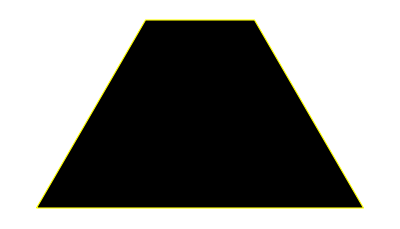

```mathematica
(*Polígonos iniciales*)
	(*Trapecio*)
axiom:=Polygon[{{0,0},{√3,0},{(2 √3)/3,1},{(√3)/3,1}}]
	(*Cuadrado*)
(*axiom:=Polygon[{{0,0},{1,0},{1,1},{0,1}}]*)
	(*Flecha*)
(*axiom:=Polygon[{{0,0},{1,1},{1,0},{0,1}}]*)

(*Traslaciones *)
tr1:={{-1,0},{0,-1}}
tr2:={{Cos[Pi/3],-Sin[Pi/3]},{Sin[Pi/3],Cos[Pi/3]}}
tr3:={{Cos[(2Pi)/3],-Sin[(2Pi)/3]},{Sin[(2Pi)/3],Cos[(2Pi)/3]}}

(*Sistema de funciones iteradas*)
next[prev_]:=prev/.Polygon[{p1_,p2_,p3_, p4_}]:>{Polygon[{p1/3,p2/3,p3/3,p4/3}],Polygon[{(tr1.p1)/3+{5/(3 √3),1/3},(tr1.p2)/3+{5/(3 √3),1/3},(tr1.p3)/3+{5/(3 √3),1/3},(tr1.p4)/3+{5/(3 √3),1/3}}],
Polygon[{p1/3+{4/(3 √3),0},p2/3+{4/(3 √3),0},p3/3+{4/(3 √3),0},p4/3+{4/(3 √3),0}}],
Polygon[{(tr3.p1)/3+{√3,0},(tr3.p2)/3+{√3,0},(tr3.p3)/3+{√3,0},(tr3.p4)/3+{√3,0}}],
Polygon[{(-tr3.p1)/3+{5/(3 √3),2/3},(-tr3.p2)/3+{5/(3 √3),2/3},(-tr3.p3)/3+{5/(3 √3),2/3},(-tr3.p4)/3+{5/(3 √3),2/3}}],
Polygon[{p1/3+{4/(3 √3),2/3},p2/3+{4/(3 √3),2/3},p3/3+{4/(3 √3),2/3},p4/3+{4/(3 √3),2/3}}],
Polygon[{(tr2.p1)/3+{7/(6 √3),1/2},(tr2.p2)/3+{7/(6 √3),1/2},(tr2.p3)/3+{7/(6 √3),1/2},(tr2.p4)/3+{7/(6 √3),1/2}}],
Polygon[{(-tr2.p1)/3+{5/(6 √3),5/6},(-tr2.p2)/3+{5/(6 √3),5/6},(-tr2.p3)/3+{5/(6 √3),5/6},(-tr2.p4)/3+{5/(6 √3),5/6}}]};
(*Funcion para dibujar el fractal*)
draw[n_]:=Graphics[{EdgeForm[Yellow],Nest[next,N@axiom,n]}];
draw[0]
```

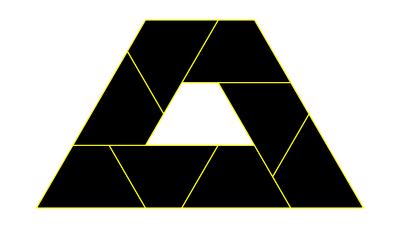

```mathematica
draw[1]
```

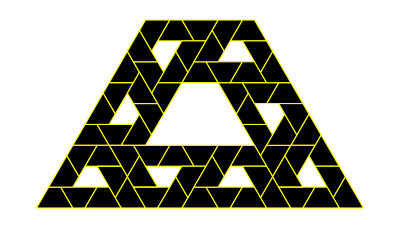

```mathematica
draw[2]
```

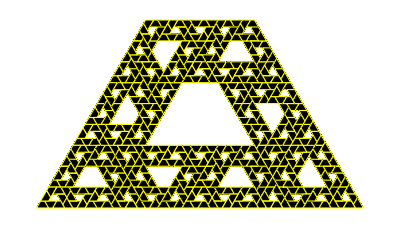

```mathematica
draw[3]
```

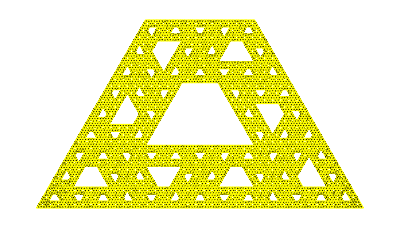

```mathematica
draw[4]
```

```mathematica
draw[5]
```

-Graphics-

```mathematica
(*
	Son similitudes de constante 1/3. La dimensión de similaridad es:
		8(1/3)^s=1 --> (1/3)^s=1/8 --> 1/3^s=1/8 --> 3^s=8 --> s=(Log 8)/(Log 3)
*)
```